# Lesson 6: Continuity

## Exercise 1 - Polynomial

```mathematica
f[x_]:=4 x^8+7 x^4+9
```

```mathematica
f[11]
```

857538020

```mathematica
Limit[f[x],x->11]==f[11]
```

True

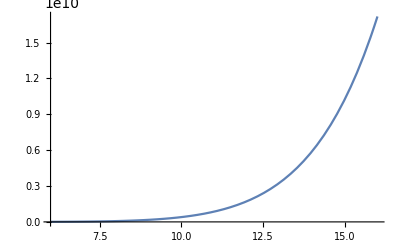

```mathematica
Plot[f[x],{x,6,16}]
```

## Exercise 2 - Rational Function

```mathematica
f[x_]:=(5 x^4+7 x^2+10)/(x^3-2x-10)
```

```mathematica
f[5]
```

662/21

```mathematica
Limit[f[x],x->5] ==f[5]
```

True

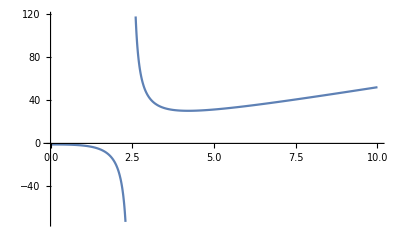

```mathematica
Plot[f[x],{x,0,10}]
```

## Exercise 3 - Finding Discontinuities

```mathematica
f[x_]:=x/(x^2-1)
```

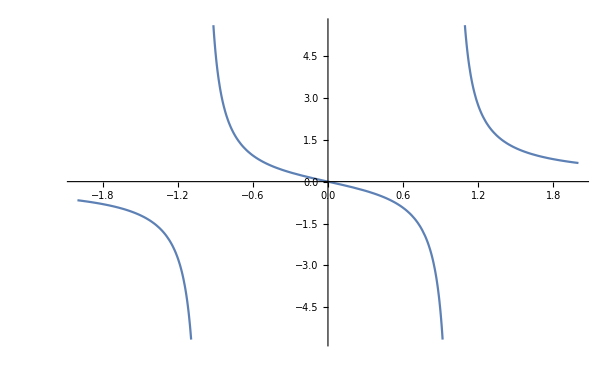

```mathematica
Plot[f[x],{x,-2,2}]
```

```mathematica
{Limit[f[x],x->-1]===f[-1],
Limit[f[x],x->1]===f[1]} //Quiet
```

{False,False}

## Exercise 4 - Finding Discontinuities

```mathematica
f[x_]:=(x^4-10 x^3+35 x^2-50x+24)/(x^2-5x+6)
```

```mathematica
Factor[x^2-5x+6]
```

(-3+x) (-2+x)

```mathematica
{Limit[f[x],x->2]==f[2],
Limit[f[x],x->3]==f[3]}//Quiet
```

{Indeterminate==ComplexInfinity,Indeterminate==ComplexInfinity}

```mathematica
Solve[x^2-5x+6==0,x]
```

{{x→2},{x→3}}

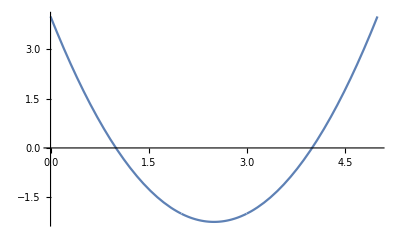

```mathematica
Plot[f[x],{x,0,5}]
```

## Exercise 5 - Trig Functions

```mathematica
f[x_]:=1/(1+Cos[x])
```

```mathematica
f[0]
```

1/2

```mathematica
Limit[f[x],x->0]==1/2
```

True

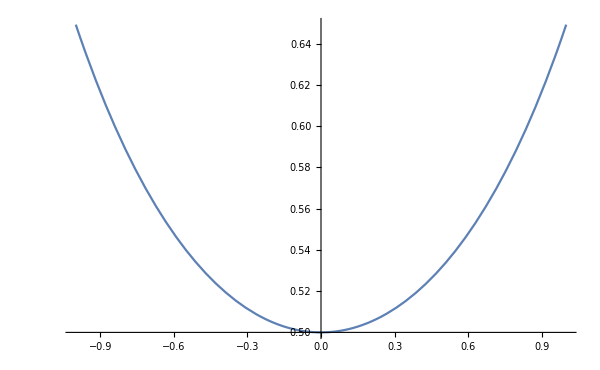

```mathematica
Plot[f[x],{x,-1,1}]
```

## Exercise 6 - Composition

```mathematica
f[x_]:=Sin[Cos[x^4]]
```

```mathematica
f[2]
```

Sin[Cos[16]]

```mathematica
Limit[f[x],x->2]==f[2]
```

True

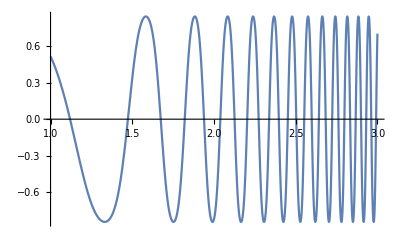

```mathematica
Plot[f[x],{x,1,3}]
```

## Exercise 7 - Intermediate Value Theorem

```mathematica
f[x_]:=x^6+6x+4
```

```mathematica
f[{-1,0}]
```

{-1,4}

Since -1 < 0 <5, there is a root in the region.

```mathematica
Solve[f[x]==0&& -1 ≤x≤4,x]//N
```

{{x→-0.683688}}

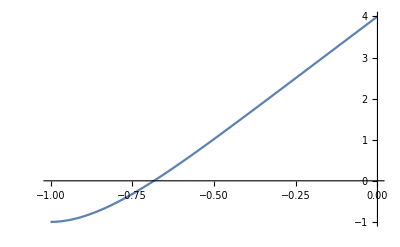

```mathematica
Plot[f[x],{x,-1,0}]
```

## Exercise 8 - Gravitational Force

```mathematica
force[r_]:=Piecewise[{{G M r/R^3,r<R}},
G M/r^2]
G = G;
```

```mathematica
M = 5.9721986`8.*^24;
R = 3958.7608367135926191043`7.;
```

```mathematica
force[R]==Limit[force[r],r->R]
```

True

```mathematica
force[r_]:=Piecewise[{{G M r/R^3,r<R}},G M/r^2]
G=Quantity[1,"GravitationalConstant"];
M=5.9721986`8.*^24;
R=3958.7608367135926191043`7.;
```

```mathematica
Plot[force[r],{r,0,2 R}]
```

-Graphics-